```mathematica
circulo={{Yellow,Disk[{1,0},2]},{Red,Circle[{-1/3,0},2/3]},Circle[{1,0},2],Circle[{1,0},1],Circle[{1,0},2/3],Circle[{1,0},1+1/3],Circle[{1,0},1+2/3],{Red,Point[{1,0}]},{Red,Point[{-7/15,-4/15}]}}
```

{{RGBColor[1, 1, 0],Disk[{1,0},2]},{RGBColor[1, 0, 0],Circle[{-1/3,0},2/3]},Circle[{1,0},2],Circle[{1,0},1],Circle[{1,0},2/3],Circle[{1,0},4/3],Circle[{1,0},5/3],{RGBColor[1, 0, 0],Point[{1,0}]},{RGBColor[1, 0, 0],Point[{-7/15,-4/15}]}}

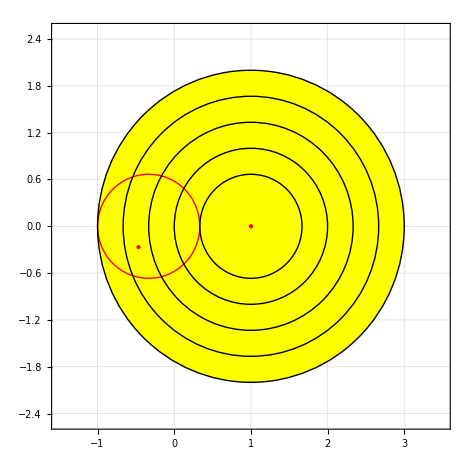

```mathematica
Graphics[circulo,GridLines->Automatic,Frame->True,PlotRange->{{-1.5,3.5},{-2.5,2.5}}]
```

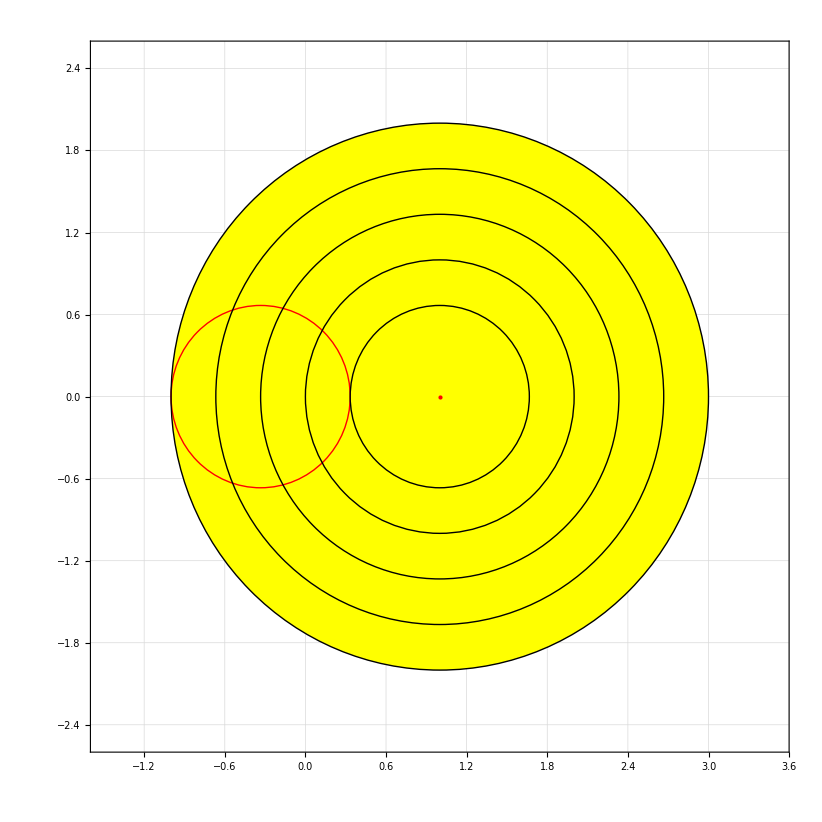

```mathematica
Show[%71,Axes->True]
```

```mathematica
Export["C:\\Users\\Víctor\\Desktop\\TFM\\circSch.png",%72,"PNG"]
```

C:\Users\Víctor\Desktop\TFM\circSch.png

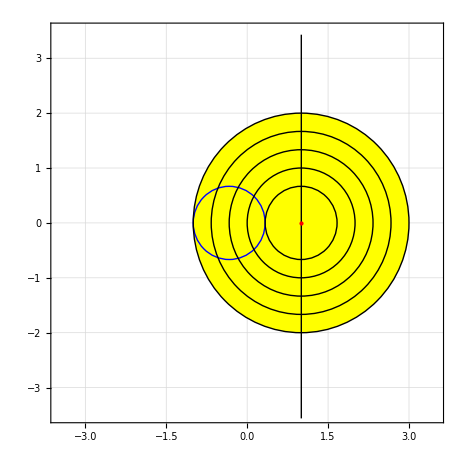

```mathematica
Show[%56,Axes->True,AxesStyle->Black]
```

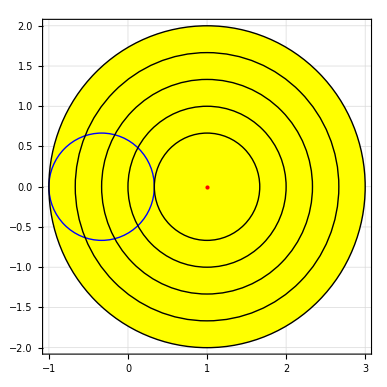

```mathematica
Show[%57]
```

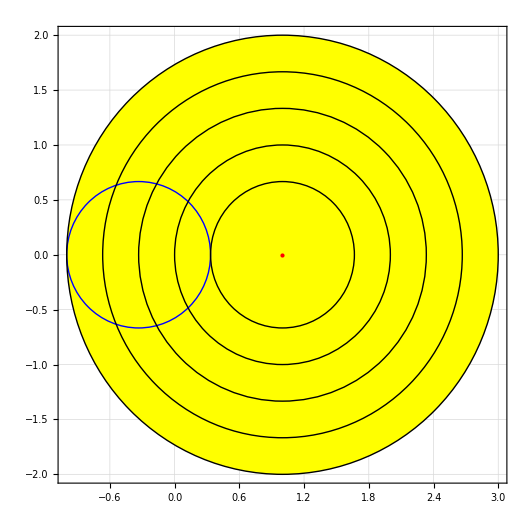
```mathematica
-Graphics-
Plot[circulo,{x,-1.5,3.5}]
```

-Graphics-

-Graphics-

```mathematica
f[x_]:= (2*Pi/30)x-Pi/3
For[x=0,x≤10,x++, Print[f[x]]]
```

0-π/3

1-(4 π)/15

2-π/5

3-(2 π)/15

4-π/15

50

6 π/15

7(2 π)/15

8 π/5

9(4 π)/15

10 π/3

```mathematica
z[x_]=2/3Exp[2Pi*x/100*I]-1/3
For[x=0,x≤10,x++, Print[z[f[x]]]]
F[z_]=(z+1/z)(1/2)
```

-1/3+2/3 ⅇ^((ⅈ π x)/50)

1/2 (1/z+z)

```mathematica
Evaluate[F[z[50]]]
```

-1

```mathematica
F[-2]
```

-5/4

```mathematica
Evaluate[ArcCos[1/2]]
```

π/3

```mathematica
Evaluate[z[ArcCos[1/2]]]
```

-1/3+2/3 ⅇ^((ⅈ π^2)/150)